```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

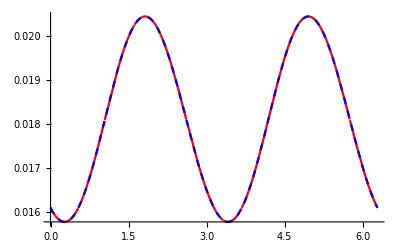

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -(ⅈ (0.+0. ⅈ) ComplexInfinity)/(4 π) encountered.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

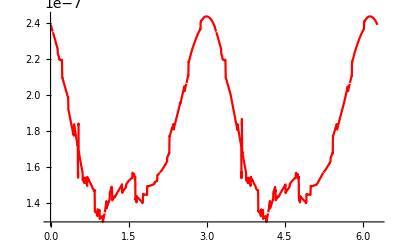

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

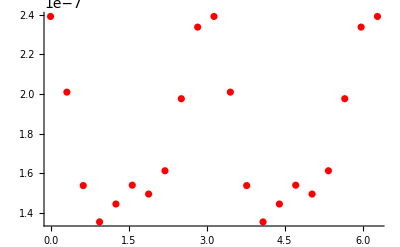

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
Clear[showdσ];
showdσ[bu_,x1u_,x3u_,kT_,showQ_:True, qSize_:0.05]:=Module[{ϕ,x2u,x4u,v2,sig},
x2u=-x1u;x4u=-x3u;
sig=NIntegrate[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
If[showQ,
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[qSize],Blue,Point[x3u]}],Graphics[{PointSize[qSize],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[qSize],Blue,Point[bu+x1u]}],Graphics[{PointSize[qSize],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[1/sig dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[1/sig dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
];
v2=1/sig NIntegrate[dσ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}];
Print["v_2=",v2];
{sig,v2}
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True, qSize_:0.05]:=Module[{ϕ,x2u,x4u,p1,p2,p3, sig,r1,r2},
x2u=-x1u;x4u=-x3u;
sig=NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
If[showQ,
r1=1/2 Sqrt[Total[(x2u-x1u)^2]];r2=1/2 Sqrt[Total[(x4u-x3u)^2]];
p1=Show[Graphics[{Orange,Opacity[0.7],Circle[{0,0},r2]}],Graphics[{Orange,Opacity[0.7],Circle[bu,r1]}],(*Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],*)Graphics[{PointSize[qSize],Blue,Point[x3u]}],Graphics[{PointSize[qSize],Red,Point[x4u]}],(*Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],*)Graphics[{PointSize[qSize],Blue,Point[bu+x1u]}],Graphics[{PointSize[qSize],Red,Point[bu+x2u]}],PlotLabel->"Dipole Orientation"];
p2=Plot[1/sig dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[1/sig dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
{sig,NIntegrate[dσHZ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/sig}
]
```

## Symmetries

```mathematica
Clear[dsigdϕ];
dsigdϕ[{θ1_,θ2_,θb_},{r1_,r2_,b_},kT_,ϕ_,showQ_ :False]:=Module[{x1u,x2u,x3u,x4u,bu,qSize},
x1u=r1{Cos[θ1],Sin[θ1]};
x3u=r2{Cos[θ2],Sin[θ2]};
x2u=-x1u;x4u=-x3u;
bu=b{Cos[θb],Sin[θb]};
If[showQ,
qSize=0.02;
Print[Show[Graphics[{Orange,Opacity[0.7],Circle[{0,0},r2]}],Graphics[{Orange,Opacity[0.7],Circle[bu,r1]}],(*Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],*)Graphics[{PointSize[qSize],Blue,Point[x3u]}],Graphics[{PointSize[qSize],Red,Point[x4u]}],(*Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],*)Graphics[{PointSize[qSize],Blue,Point[bu+x1u]}],Graphics[{PointSize[qSize],Red,Point[bu+x2u]}]]];
];
dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]
]
```

### Rotational symmetry of the whole system

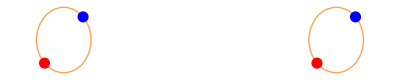

9.27326×10^-6

```mathematica
dsigdϕ[{π/4,π/4,0},{0.1,0.1,1.0},1.0,0.2,True]
```

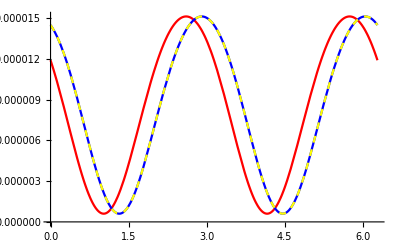

```mathematica
Plot[{dsigdϕ[{π/4,π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π/4+δϕ,π/4+δϕ,0+δϕ},{0.1,0.1,1.0},1.0,ϕ]/.{δϕ->0.3},dsigdϕ[{π/4,π/4,0},{0.1,0.1,1.0},1.0,ϕ-δϕ]/.{δϕ->0.3}},{ϕ,0,2π},PlotStyle->{{Red}, {Blue}, {Yellow,Dashed}}]
```

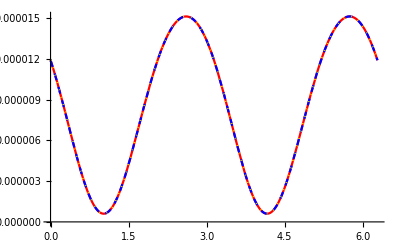

```mathematica
Plot[{dsigdϕ[{π/4,π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π/4+δϕ,π/4+δϕ,0+δϕ},{0.1,0.1,1.0},1.0,ϕ]/.{δϕ->π},dsigdϕ[{π/4,π/4,0},{0.1,0.1,1.0},1.0,ϕ-δϕ]/.{δϕ->π}},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}, {Yellow,Dotted}}]
```

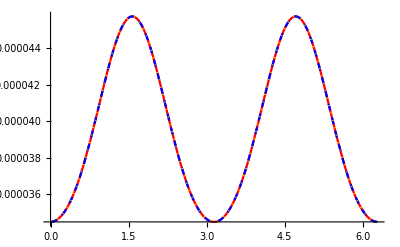

```mathematica
Plot[{dsigdϕ[{π/4,-π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π/4+δϕ,-π/4+δϕ,0+δϕ},{0.1,0.1,1.0},1.0,ϕ]/.{δϕ->π},dsigdϕ[{π/4,-π/4,0},{0.1,0.1,1.0},1.0,ϕ-δϕ]/.{δϕ->π}},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}, {Yellow,Dotted}}]
```

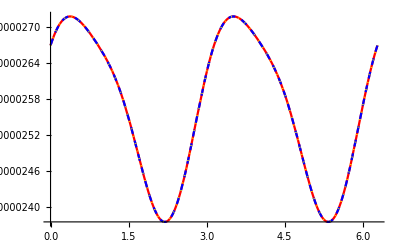

```mathematica
Plot[{dsigdϕ[{π/14,-π/3,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π/14+δϕ,-π/3+δϕ,0+δϕ},{0.1,0.1,1.0},1.0,ϕ]/.{δϕ->π},dsigdϕ[{π/14,-π/3,0},{0.1,0.1,1.0},1.0,ϕ-δϕ]/.{δϕ->π}},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}, {Yellow,Dotted}}]
```

### x_1<->x_2 or x_3<->x_4

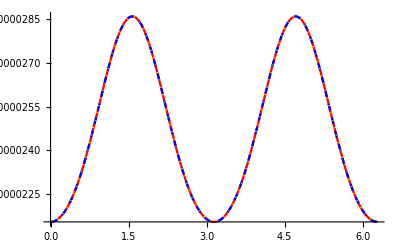

```mathematica
Plot[{dsigdϕ[{π/4,-π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π/4,-π/4,0},{-0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π/4,-π/4,0},{0.1,-0.1,1.0},1.0,ϕ]},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}, {Yellow,Dotted}}]
```

### x_1<->x_3 and x_2<->x_4

```mathematica
gauge[{r1_,θ1_},{r2_,θ2_},{b_,θb_},{kT_,ϕ_},showQ_ :False,qSize_:0.02]:=Module[{x1u,x2u,x3u,x4u,bu},
x1u=r1{Cos[θ1],Sin[θ1]};
x3u=r2{Cos[θ2],Sin[θ2]};
x2u=-x1u;x4u=-x3u;
bu=b{Cos[θb],Sin[θb]};
If[showQ,
Print[Show[Graphics[{Orange,Opacity[0.7],Circle[{0,0},r2]}],Graphics[{Orange,Opacity[0.7],Circle[bu,r1]}],(*Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],*)Graphics[{PointSize[qSize],Blue,Point[x3u]}],Graphics[{PointSize[qSize],Red,Point[x4u]}],(*Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],*)Graphics[{PointSize[qSize],Blue,Point[bu+x1u]}],Graphics[{PointSize[qSize],Red,Point[bu+x2u]}]]];
];
dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]/dσHZ[bu+x3u,bu+x4u,x1u,x2u,{kT,ϕ}]
]
```

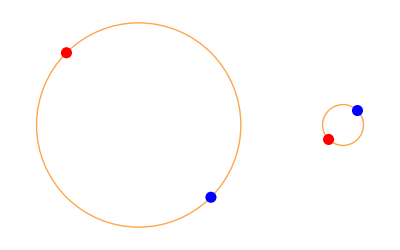

-2.07509×10^-10

```mathematica
gauge[{0.1,π/4},{0.5,-π/4},{1,0},{1.0,0.01},True]
```

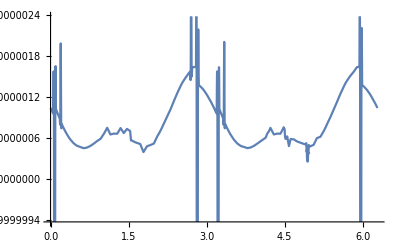

```mathematica
Plot[{gauge[{0.1,π/545},{0.5,-π/8},{1,0},{1.0,ϕ}]},{ϕ,0,2π}]
```

### Reflection symmetries

#### Over the x - axis

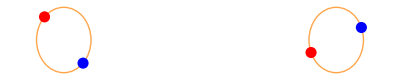

0.0000388015

```mathematica
dsigdϕ[{π/8,-π/4,0},{0.1,0.1,1.0},1.0,0,True]
```

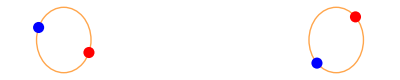

0.0000388015

```mathematica
dsigdϕ[{π+π/4,π-π/8,0},{0.1,0.1,1.0},1.0,0,True]
```

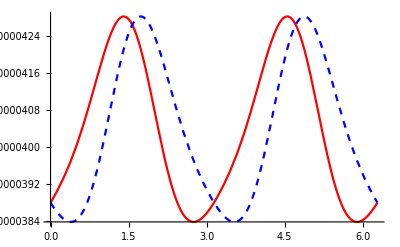

```mathematica
Plot[{dsigdϕ[{π/8,-π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π+π/4,π-π/8,0},{0.1,0.1,1.0},1.0,ϕ]},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}}]
```

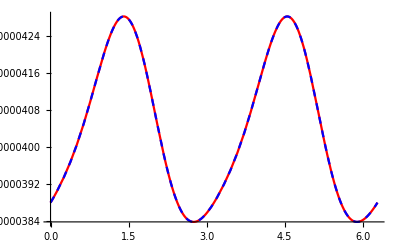

```mathematica
Plot[{dsigdϕ[{π/8,-π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{π+π/4,π-π/8,0},{0.1,0.1,1.0},1.0,π-ϕ]},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}}]
```

#### Over the y - axis

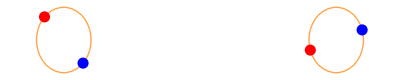

0.0000385244

```mathematica
dsigdϕ[{π/10,-π/4,0},{0.1,0.1,1.0},1.0,0,True]
```

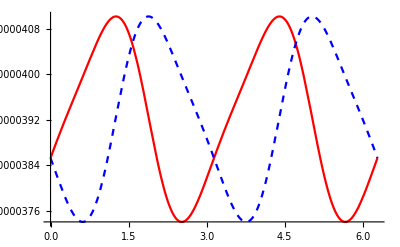

```mathematica
Plot[{dsigdϕ[{π/10,-π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{-π/10,π/4,0},{0.1,0.1,1.0},1.0,ϕ]},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}}]
```

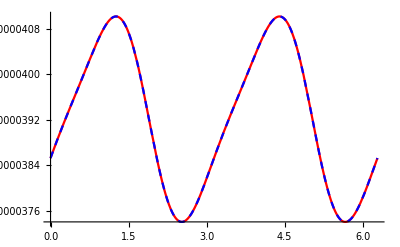

```mathematica
Plot[{dsigdϕ[{π/10,-π/4,0},{0.1,0.1,1.0},1.0,ϕ],dsigdϕ[{-π/10,π/4,0},{0.1,0.1,1.0},1.0,-ϕ]},{ϕ,0,2π},PlotStyle->{{Red}, {Blue,Dashed}}]
```

## b = 1

### r = 1

#### kT = 0.1

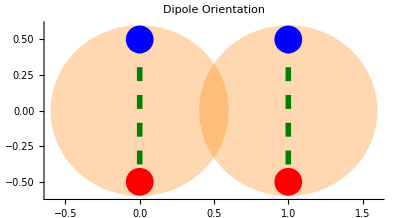

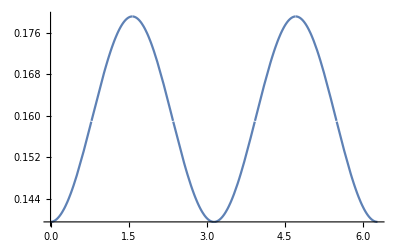

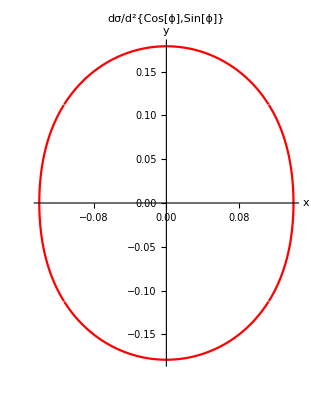

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2084974 near {ϕ$2084974} = {0.0000241858}. NIntegrate obtained 1.99764×10^-17+0. ⅈ and 7.92985×10^-17 for the integral and error estimates.

v_2={-0.0620339+0. ⅈ,8.48684×10^-17}

{-0.0620339+0. ⅈ,8.48684×10^-17}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.5;
showdσ[bu,x1u,x3u,kT]
```

-Graphics-

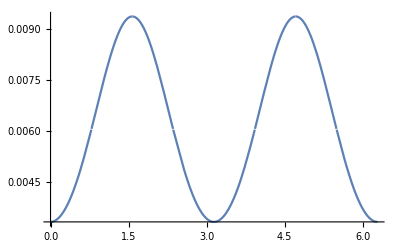

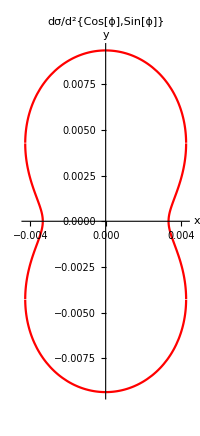

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25405840 near {ϕ$25405840} = {0.0000241858}. NIntegrate obtained 1.32679×10^-17+0. ⅈ and 7.44428×10^-18 for the integral and error estimates.

v_2={-0.242273+0. ⅈ,3.40479×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

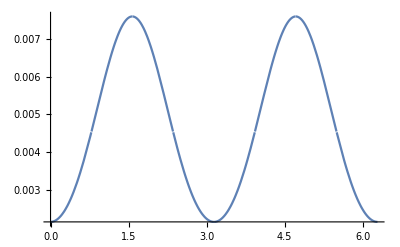

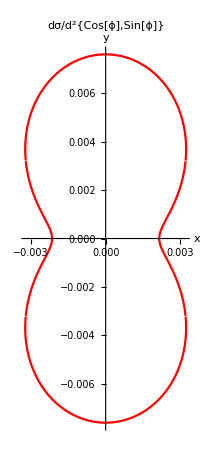

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25803385 near {ϕ$25803385} = {2.25792}. NIntegrate obtained 2.10742×10^-18+0. ⅈ and 2.52612×10^-18 for the integral and error estimates.

v_2={-0.289532+0. ⅈ,7.12635×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.1;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

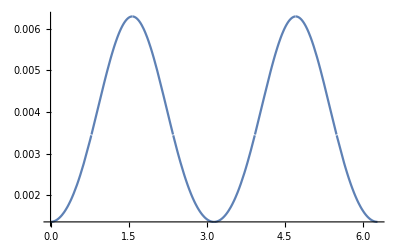

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26188966 near {ϕ$26188966} = {1.14118}. NIntegrate obtained -3.07642×10^-18+0. ⅈ and 1.99011×10^-18 for the integral and error estimates.

v_2={-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.2;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

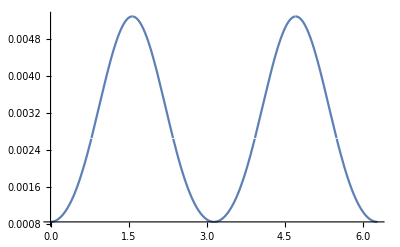

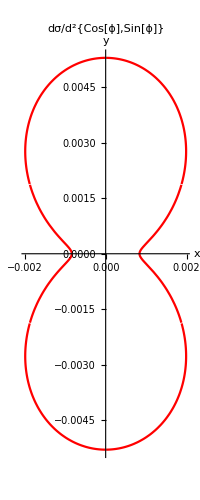

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26566626 near {ϕ$26566626} = {0.822116}. NIntegrate obtained -2.18196×10^-18+0. ⅈ and 1.50195×10^-18 for the integral and error estimates.

v_2={-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.3;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

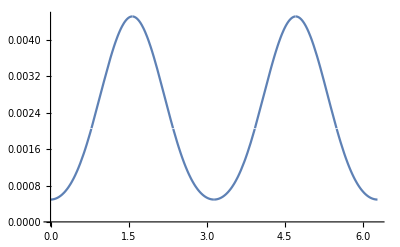

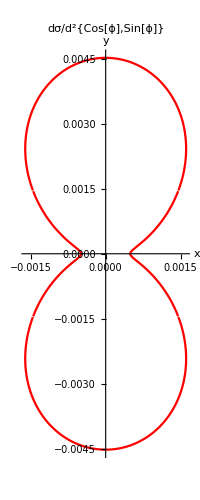

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26944030 near {ϕ$26944030} = {2.28247}. NIntegrate obtained -2.71051×10^-18+0. ⅈ and 1.47598×10^-18 for the integral and error estimates.

v_2={-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.4;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

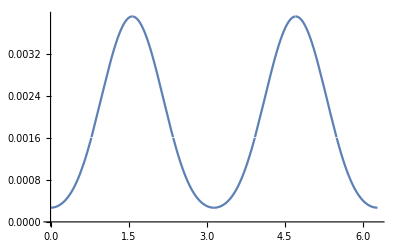

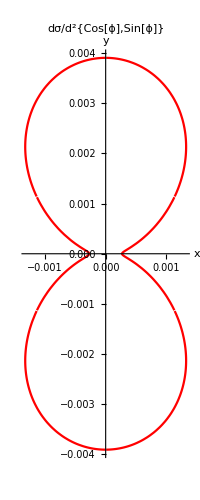

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$27342164 near {ϕ$27342164} = {0.920291}. NIntegrate obtained 9.21572×10^-19+0. ⅈ and 1.07721×10^-18 for the integral and error estimates.

v_2={-0.493546+0. ⅈ,7.943×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

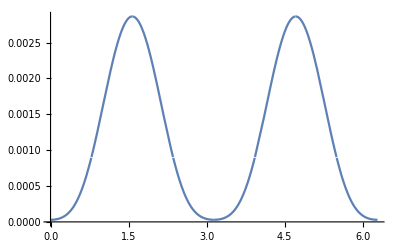

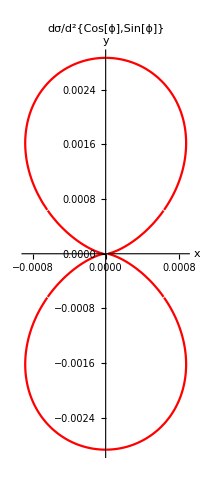

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$27727248 near {ϕ$27727248} = {0.858932}. NIntegrate obtained 2.29377×10^-18+0. ⅈ and 8.5747×10^-19 for the integral and error estimates.

v_2={-0.606603+0. ⅈ,3.11017×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

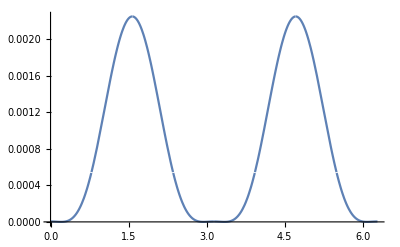

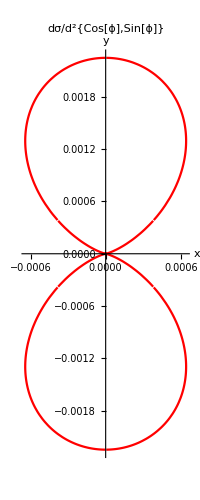

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$28119092 near {ϕ$28119092} = {1.178}. NIntegrate obtained -1.53912×10^-18+0. ⅈ and 5.68968×10^-19 for the integral and error estimates.

v_2={-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

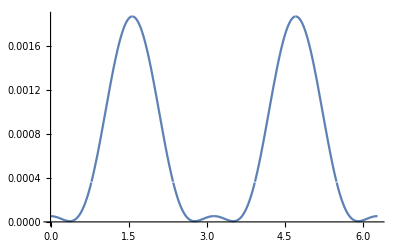

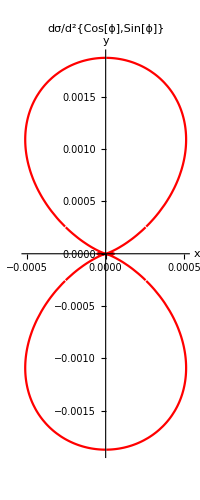

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$28582005 near {ϕ$28582005} = {2.23338}. NIntegrate obtained -1.34509×10^-18+0. ⅈ and 5.32879×10^-19 for the integral and error estimates.

v_2={-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

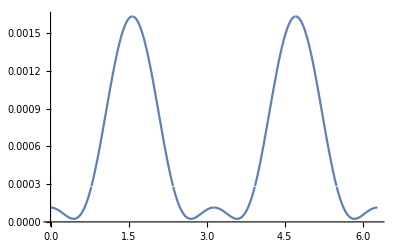

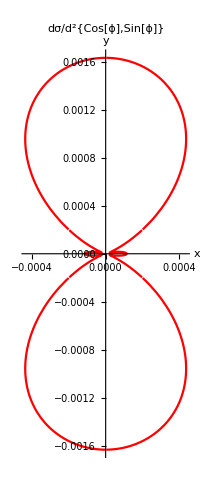

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$29074717 near {ϕ$29074717} = {2.25792}. NIntegrate obtained 7.7927×10^-20+0. ⅈ and 4.92233×10^-19 for the integral and error estimates.

v_2={-0.664932+0. ⅈ,2.14288×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

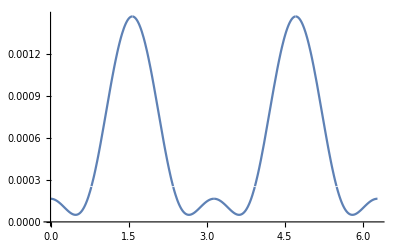

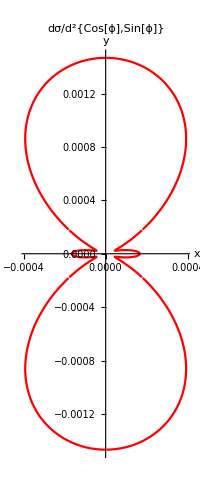

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$29568935 near {ϕ$29568935} = {2.06157}. NIntegrate obtained -1.01983×10^-18+0. ⅈ and 5.71921×10^-19 for the integral and error estimates.

v_2={-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

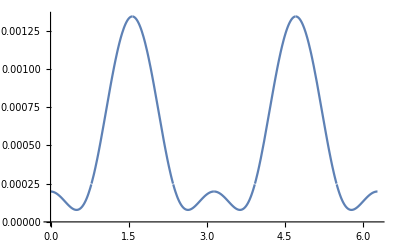

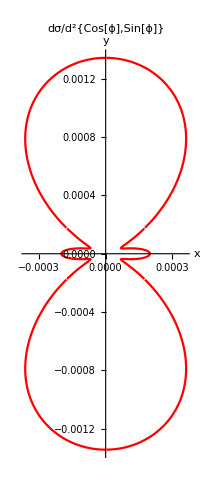

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30090867 near {ϕ$30090867} = {2.01249}. NIntegrate obtained -4.06576×10^-19+0. ⅈ and 5.09201×10^-19 for the integral and error estimates.

v_2={-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

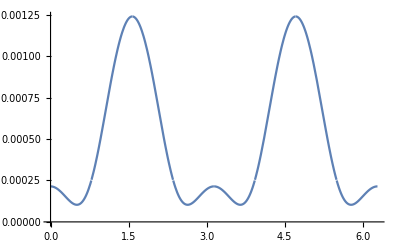

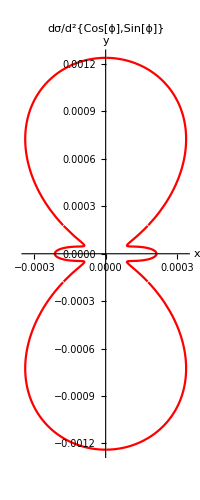

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30617974 near {ϕ$30617974} = {0.0000241858}. NIntegrate obtained -6.33157×10^-19+0. ⅈ and 1.03203×10^-18 for the integral and error estimates.

v_2={-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

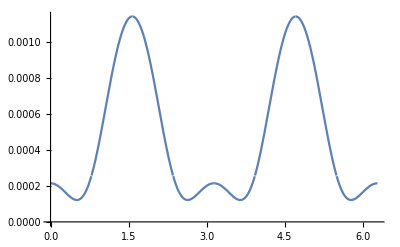

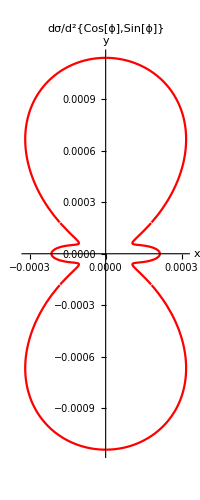

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31127020 near {ϕ$31127020} = {0.0000241858}. NIntegrate obtained 7.07061×10^-19+0. ⅈ and 1.21397×10^-18 for the integral and error estimates.

v_2={-0.501266+0. ⅈ,2.3872×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

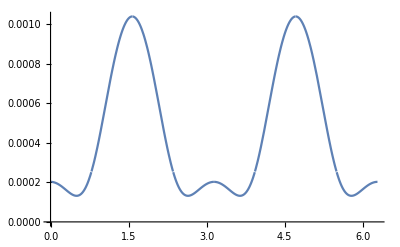

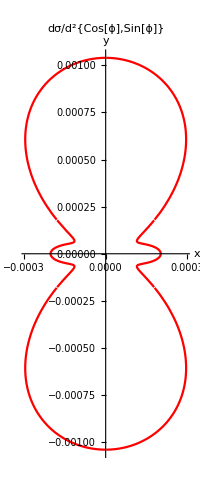

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31620722 near {ϕ$31620722} = {0.0000241858}. NIntegrate obtained -2.95106×10^-18+0. ⅈ and 1.33214×10^-18 for the integral and error estimates.

v_2={-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

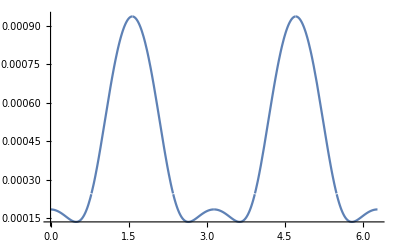

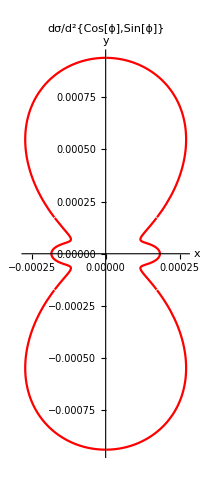

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32120680 near {ϕ$32120680} = {0.674854}. NIntegrate obtained 5.04832×10^-19+0. ⅈ and 1.31251×10^-18 for the integral and error estimates.

v_2={-0.467766+0. ⅈ,1.96087×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

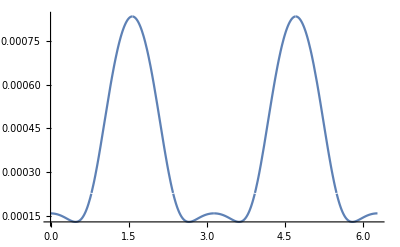

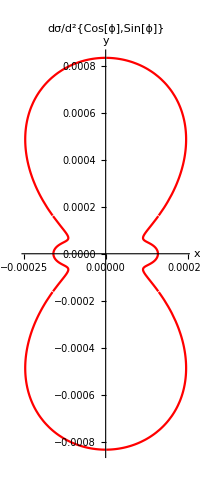

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32618210 near {ϕ$32618210} = {0.822116}. NIntegrate obtained 6.50521×10^-19+0. ⅈ and 1.71884×10^-18 for the integral and error estimates.

v_2={-0.460269+0. ⅈ,2.79431×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

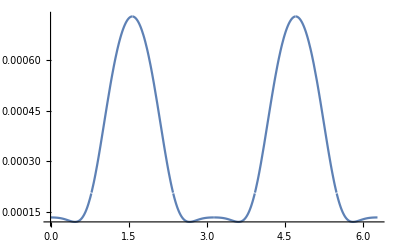

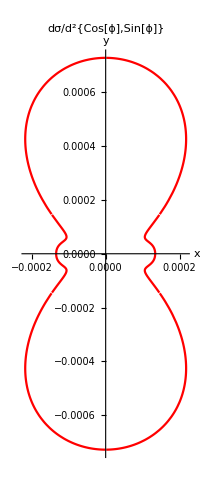

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33122676 near {ϕ$33122676} = {2.41746}. NIntegrate obtained 1.999×10^-19+0. ⅈ and 1.63337×10^-18 for the integral and error estimates.

v_2={-0.457377+0. ⅈ,9.70988×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

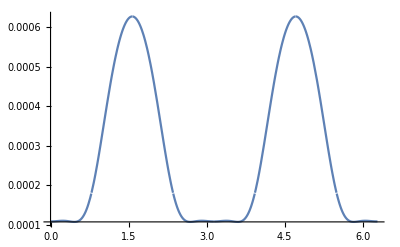

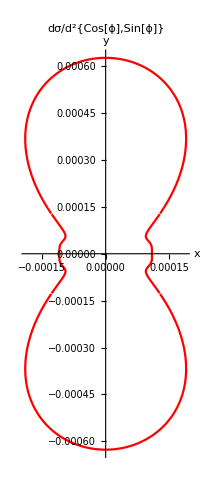

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33627852 near {ϕ$33627852} = {0.84666}. NIntegrate obtained 1.63308×10^-18+0. ⅈ and 2.74586×10^-18 for the integral and error estimates.

v_2={-0.458429+0. ⅈ,9.17943×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

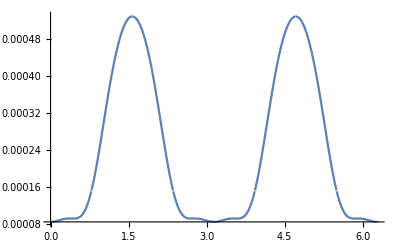

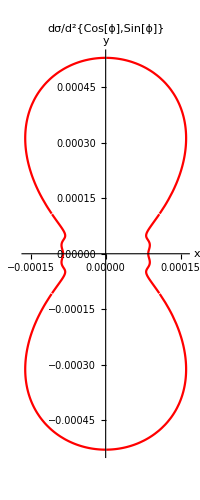

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34164679 near {ϕ$34164679} = {2.22111}. NIntegrate obtained 3.92515×10^-18+0. ⅈ and 3.18254×10^-18 for the integral and error estimates.

v_2={-0.463108+0. ⅈ,2.61457×10^-15}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

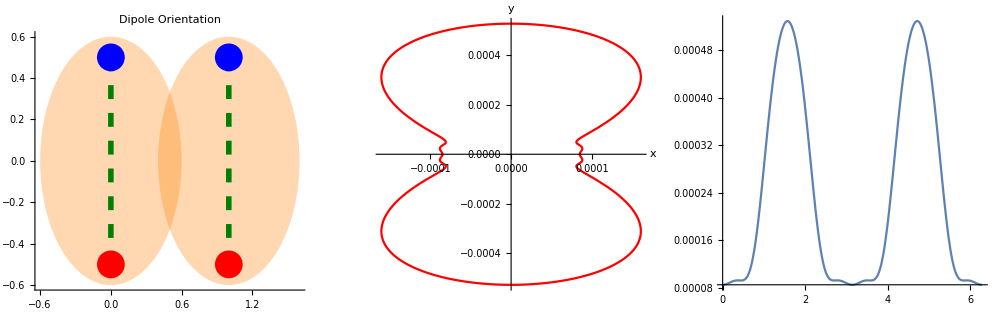

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34717038 near {ϕ$34717038} = {1.01847}. NIntegrate obtained -2.05861×10^-12 and 1.2748×10^-12 for the integral and error estimates.

{-0.463108,-1.37125×10^-9}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

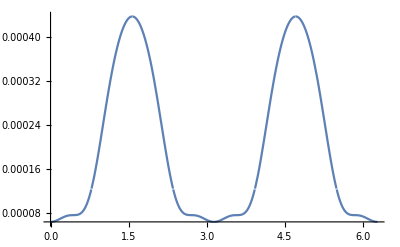

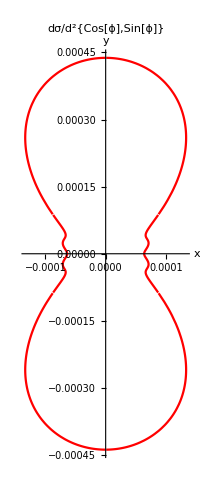

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34827593 near {ϕ$34827593} = {2.33155}. NIntegrate obtained -3.60497×10^-18+0. ⅈ and 3.26968×10^-18 for the integral and error estimates.

v_2={-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

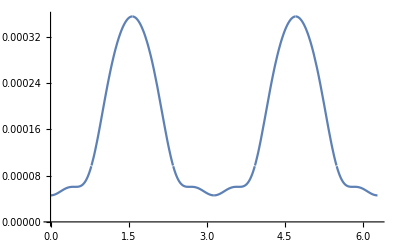

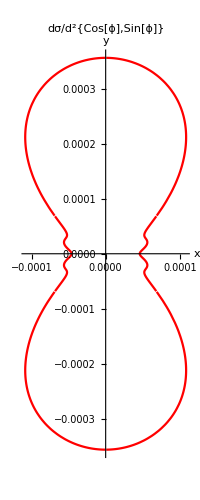

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$35363065 near {ϕ$35363065} = {2.50336}. NIntegrate obtained 2.77954×10^-18+0. ⅈ and 4.31198×10^-18 for the integral and error estimates.

v_2={-0.483405+0. ⅈ,2.80211×10^-15}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

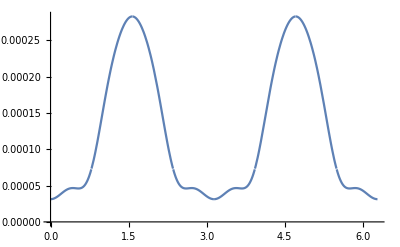

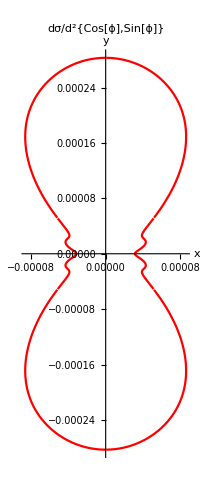

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$35901002 near {ϕ$35901002} = {0.748485}. NIntegrate obtained -2.88838×10^-19+0. ⅈ and 3.10996×10^-18 for the integral and error estimates.

v_2={-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

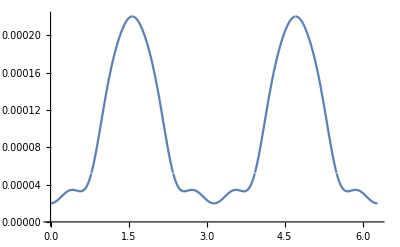

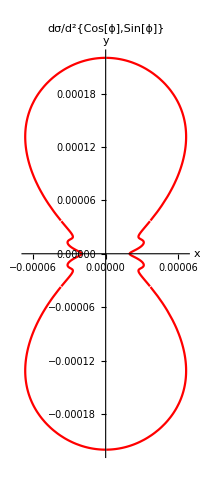

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$36441489 near {ϕ$36441489} = {2.47882}. NIntegrate obtained 5.19104×10^-18+0. ⅈ and 4.81235×10^-18 for the integral and error estimates.

v_2={-0.520401+0. ⅈ,8.82195×10^-15}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

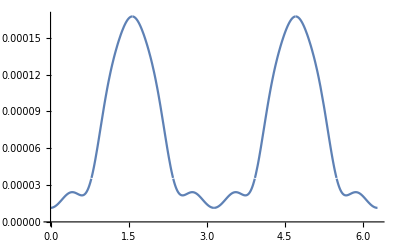

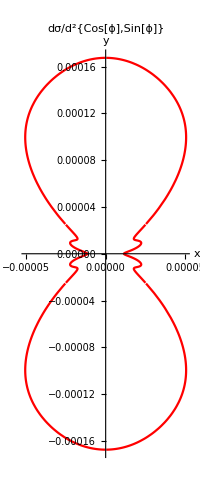

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$36989626 near {ϕ$36989626} = {0.65031}. NIntegrate obtained -2.9661×10^-18+0. ⅈ and 3.98539×10^-18 for the integral and error estimates.

v_2={-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

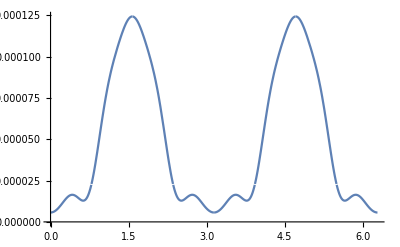

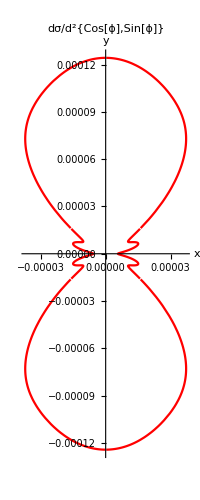

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$37544909 near {ϕ$37544909} = {2.50336}. NIntegrate obtained -3.51085×10^-18+0. ⅈ and 5.16886×10^-18 for the integral and error estimates.

v_2={-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

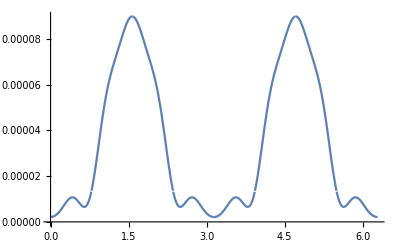

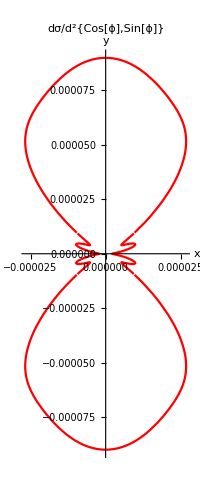

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$38107113 near {ϕ$38107113} = {2.28247}. NIntegrate obtained -1.16183×10^-17+0. ⅈ and 4.21943×10^-18 for the integral and error estimates.

v_2={-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

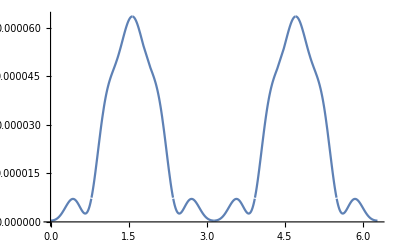

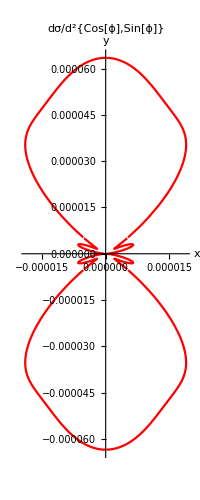

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$38658935 near {ϕ$38658935} = {0.969378}. NIntegrate obtained -1.7087×10^-17+0. ⅈ and 4.05027×10^-18 for the integral and error estimates.

v_2={-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

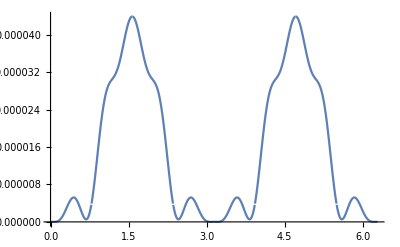

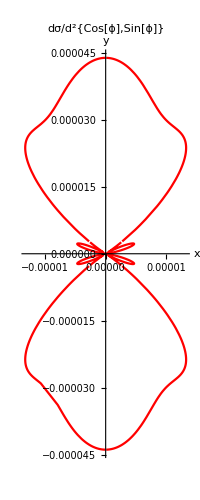

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39193941 near {ϕ$39193941} = {2.22111}. NIntegrate obtained -1.72414×10^-18+0. ⅈ and 5.36369×10^-18 for the integral and error estimates.

v_2={-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

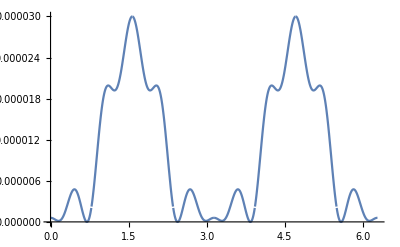

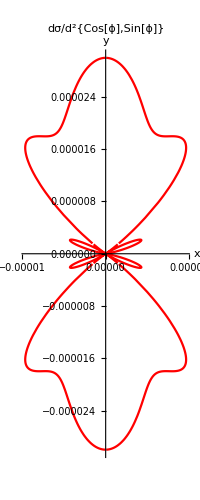

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39777025 near {ϕ$39777025} = {2.18429}. NIntegrate obtained 6.65526×10^-18+0. ⅈ and 5.09018×10^-18 for the integral and error estimates.

v_2={-0.626094+0. ⅈ,1.02341×10^-13}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

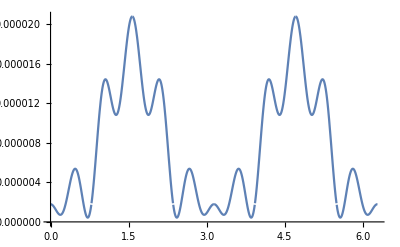

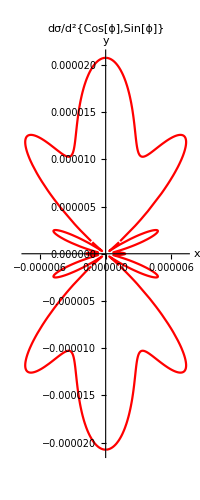

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40449219 near {ϕ$40449219} = {0.944835}. NIntegrate obtained 9.31906×10^-18+0. ⅈ and 7.58834×10^-18 for the integral and error estimates.

v_2={-0.509444+0. ⅈ,1.97668×10^-13}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

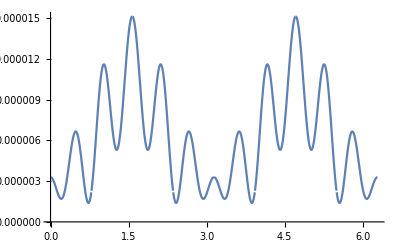

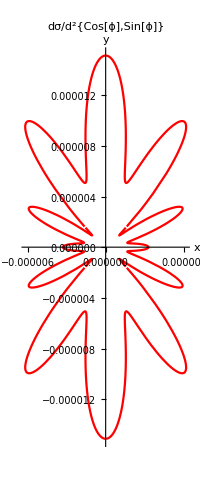

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41134787 near {ϕ$41134787} = {2.17202}. NIntegrate obtained 1.88269×10^-18+0. ⅈ and 1.04716×10^-17 for the integral and error estimates.

v_2={-0.312699+0. ⅈ,4.85387×10^-14}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

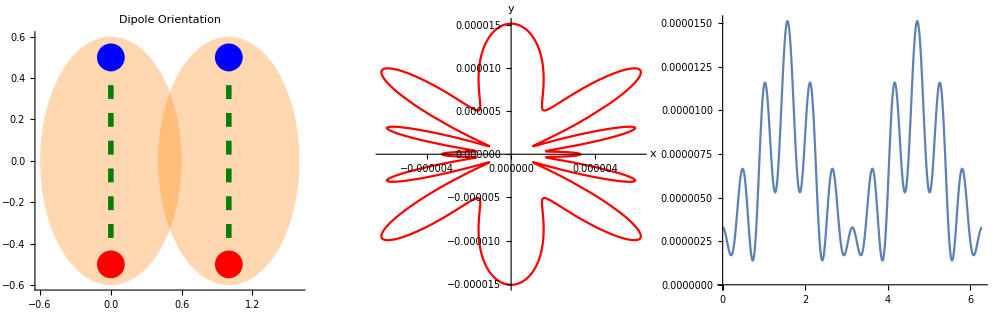

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41827073 near {ϕ$41827073} = {2.95742}. NIntegrate obtained -5.81201×10^-15 and 8.90176×10^-13 for the integral and error estimates.

{-0.3127,-1.49843×10^-10}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

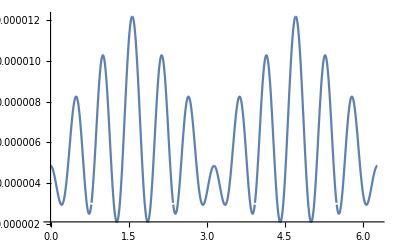

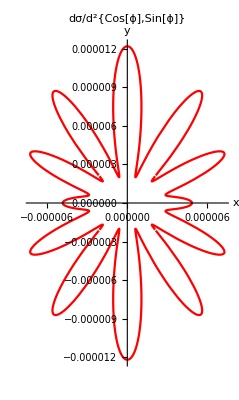

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41978991 near {ϕ$41978991} = {2.29474}. NIntegrate obtained -2.29538×10^-17+0. ⅈ and 2.02749×10^-17 for the integral and error estimates.

v_2={-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

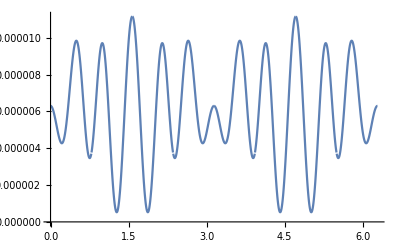

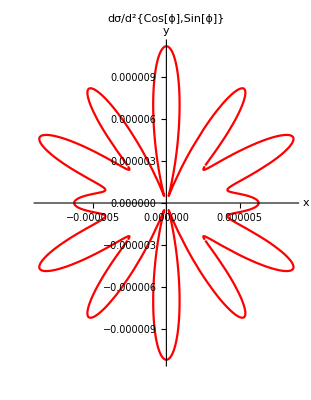

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$42666724 near {ϕ$42666724} = {0.84666}. NIntegrate obtained -4.67437×10^-17+0. ⅈ and 2.33295×10^-17 for the integral and error estimates.

v_2={0.0293956,-1.22152×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

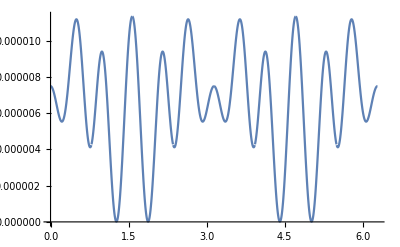

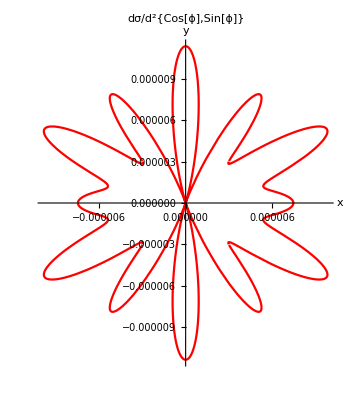

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$43343733 near {ϕ$43343733} = {2.33155}. NIntegrate obtained -1.30332×10^-17+0. ⅈ and 3.26071×10^-17 for the integral and error estimates.

v_2={0.0991137,-3.14959×10^-13+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

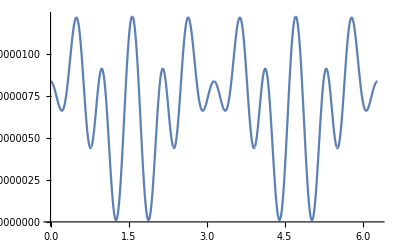

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$44022180 near {ϕ$44022180} = {2.34382}. NIntegrate obtained -2.14631×10^-16+0. ⅈ and 4.04524×10^-17 for the integral and error estimates.

v_2={0.12317,-4.81401×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$44702342 near {ϕ$44702342} = {0.883475}. NIntegrate obtained -7.23042×10^-17+0. ⅈ and 5.02032×10^-17 for the integral and error estimates.

v_2={0.123017,-1.54057×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$45387184 near {ϕ$45387184} = {0.797572}. NIntegrate obtained 7.60238×10^-17+0. ⅈ and 8.73176×10^-17 for the integral and error estimates.

v_2={0.110969,1.58621×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46070838 near {ϕ$46070838} = {2.28247}. NIntegrate obtained 8.23575×10^-17+0. ⅈ and 8.42158×10^-17 for the integral and error estimates.

v_2={0.0929297,1.73677×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46754320 near {ϕ$46754320} = {2.23338}. NIntegrate obtained -1.68858×10^-16+0. ⅈ and 7.2551×10^-17 for the integral and error estimates.

v_2={0.071308,-3.70985×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$47442360 near {ϕ$47442360} = {0.834388}. NIntegrate obtained -4.8105×10^-16+0. ⅈ and 9.63035×10^-17 for the integral and error estimates.

v_2={0.046731,-1.13229×10^-11+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48153117 near {ϕ$48153117} = {0.883475}. NIntegrate obtained -4.766×10^-17+0. ⅈ and 1.054×10^-16 for the integral and error estimates.

v_2={0.0189289,-1.23227×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48847741 near {ϕ$48847741} = {2.22111}. NIntegrate obtained 2.76484×10^-16+0. ⅈ and 1.54643×10^-16 for the integral and error estimates.

v_2={-0.0127807+0. ⅈ,8.02354×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$49551406 near {ϕ$49551406} = {2.27019}. NIntegrate obtained 8.69857×10^-16+0. ⅈ and 1.92874×10^-16 for the integral and error estimates.

v_2={-0.0491407+0. ⅈ,2.88322×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}}}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50255325 near {ϕ$50255325} = {3.706}. NIntegrate obtained -1.48263×10^-6 and 3.52391×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50255325 near {ϕ$50255325} = {3.706}. NIntegrate obtained -2.65441×10^-14 and 1.937×10^-12 for the integral and error estimates.

{-0.0491431,-8.79825×10^-10}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50361508 near {ϕ$50361508} = {0.957106}. NIntegrate obtained 2.15498×10^-16+0. ⅈ and 1.93393×10^-16 for the integral and error estimates.

v_2={-0.0905752+0. ⅈ,8.26214×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$51067207 near {ϕ$51067207} = {2.24565}. NIntegrate obtained -4.3545×10^-17+0. ⅈ and 2.32221×10^-16 for the integral and error estimates.

v_2={-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$51760150 near {ϕ$51760150} = {0.662582}. NIntegrate obtained 4.02214×10^-16+0. ⅈ and 4.00041×10^-16 for the integral and error estimates.

v_2={-0.185819+0. ⅈ,2.09273×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52459132 near {ϕ$52459132} = {0.760757}. NIntegrate obtained -3.77966×10^-16+0. ⅈ and 5.30339×10^-16 for the integral and error estimates.

v_2={-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$53150249 near {ϕ$53150249} = {0.748485}. NIntegrate obtained 5.79877×10^-16+0. ⅈ and 6.93605×10^-16 for the integral and error estimates.

v_2={-0.277796+0. ⅈ,3.9952×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$53843153 near {ϕ$53843153} = {2.42973}. NIntegrate obtained -1.80718×10^-15+0. ⅈ and 9.42879×10^-16 for the integral and error estimates.

v_2={-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$54531737 near {ϕ$54531737} = {2.38064}. NIntegrate obtained -1.80047×10^-15+0. ⅈ and 1.92618×10^-15 for the integral and error estimates.

v_2={-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55221973 near {ϕ$55221973} = {2.29474}. NIntegrate obtained 2.86021×10^-15+0. ⅈ and 1.53065×10^-15 for the integral and error estimates.

v_2={-0.328691+0. ⅈ,2.66774×10^-10}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}}}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55926032 near {ϕ$55926032} = {5.03136}. NIntegrate obtained 8.34509×10^-15 and 4.27678×10^-13 for the integral and error estimates.

{-0.328691,7.78354×10^-10}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56070345 near {ϕ$56070345} = {2.39291}. NIntegrate obtained -1.29258×10^-14+0. ⅈ and 3.2129×10^-15 for the integral and error estimates.

v_2={-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56786507 near {ϕ$56786507} = {2.49109}. NIntegrate obtained 6.77554×10^-16+0. ⅈ and 3.01841×10^-15 for the integral and error estimates.

v_2={-0.284242+0. ⅈ,7.26712×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$57502891 near {ϕ$57502891} = {0.736213}. NIntegrate obtained 4.67769×10^-15+0. ⅈ and 4.33086×10^-15 for the integral and error estimates.

v_2={-0.244547+0. ⅈ,5.35399×10^-10}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58215605 near {ϕ$58215605} = {0.748485}. NIntegrate obtained 3.70163×10^-15+0. ⅈ and 8.24761×10^-15 for the integral and error estimates.

v_2={-0.197058+0. ⅈ,4.53068×10^-10}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65104689 near {ϕ$65104689} = {2.27019}. NIntegrate obtained -7.39578×10^-14+0. ⅈ and 2.2683×10^-14 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8. Sin[ϕ$65104689])) (-(1+ⅇ^(ⅈ (0.-16. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]-(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]-(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8. Sin[ϕ$65104689])) (-(1+ⅇ^(ⅈ (0.-16. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]-(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]-(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8. Sin[ϕ$65104689])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]+(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]+(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8. Sin[ϕ$65104689])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]+(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]+(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: (16. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$65104689])]))/Abs[0.-16. Sin[ϕ$65104689]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$65104689])]))/Abs[0.-16. Sin[ϕ$65104689]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

v_2={0.163312,-1.55804×10^-8+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=20;
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1473551 near {ϕ$1473551} = {2.06157}. NIntegrate obtained -3.62612×10^-7 and 1.21877×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1473551 near {ϕ$1473551} = {2.06157}. NIntegrate obtained 2.87259×10^-14 and 9.56599×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1473551 near {ϕ$1473551} = {2.06157}. NIntegrate obtained 1.50564×10^-6 and 2.38403×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-0.240835,1.90788×10^-8}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=30;
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1169166 near {ϕ$1169166} = {2.93287}. NIntegrate obtained 2.2428×10^-8 and 1.60327×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1169166 near {ϕ$1169166} = {3.86553}. NIntegrate obtained -1.77874×10^-13 and 1.52145×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1169166 near {ϕ$1169166} = {0.723941}. NIntegrate obtained 4.07688×10^-7 and 3.51317×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.0550126,-4.363×10^-7}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=40;
showdσHZ[bu,x1u,x3u,kT]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2409338 near {ϕ$2409338} = {1.92658}. NIntegrate obtained 1.28724×10^-7 and 1.61403×10^-12 for the integral and error estimates.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2409338 near {ϕ$2409338} = {5.06817}. NIntegrate obtained -2.63853×10^-10 and 9.99434×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2409338 near {ϕ$2409338} = {2.30701}. NIntegrate obtained -1.70376×10^-12 and 2.09817×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-0.00204976,-0.0000132358}

### r = 0.1

#### kT = 1

```mathematica
show[θ1_,θ2_,r0_,b_,kT_, qSize_,showQ_:True]:=Module[{x1u,x3u,bu},
x1u=r0/2{Cos[θ1],Sin[θ1]};
x3u=r0/2{Cos[θ2],Sin[θ2]};
bu={1,0};
showdσ[bu,x1u,x3u,kT,showQ,qSize]
]
```

```mathematica
show[π/2,π/2,1/10,1.0,1.0,0.02,True]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$6557807 near {ϕ$6557807} = {4.0987}. NIntegrate obtained 1.78574×10^-17 and 2.32943×10^-15 for the integral and error estimates.

{0.0000100541,{-0.240227,1.77613×10^-12}}

```mathematica
show[π/4,π/2,1/10,1.0,1.0,0.02,True]
```

-Graphics-

{6.76912×10^-6,{-0.127141,-0.0916618}}

```mathematica
show[-π/4,π/2,1/10,1.0,1.0,0.02,True]
```

-Graphics-

{6.76912×10^-6,{-0.127141,0.0916618}}

```mathematica
show[0,π/2,1/10,1.0,1.0,0.02,True]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$6822449 near {ϕ$6822449} = {1.03074}. NIntegrate obtained 1.5573×10^-18 and 1.16076×10^-15 for the integral and error estimates.

{3.38042×10^-6,{0.213592,4.60683×10^-13}}

```mathematica
show[π/2,0,1/10,1.0,1.0,0.02,True]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7046382 near {ϕ$7046382} = {1.03074}. NIntegrate obtained -1.03813×10^-18 and 7.14828×10^-16 for the integral and error estimates.

{3.38042×10^-6,{0.213592,-3.07102×10^-13}}

```mathematica
show[0,0,1/10,1.0,1.0,0.02,True]
```

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7220830 near {ϕ$7220830} = {1.10437}. NIntegrate obtained 4.10248×10^-19 and 1.47194×10^-15 for the integral and error estimates.

{0.000021147,{0.0110111,1.93998×10^-14}}

```mathematica
show[π/4,π/12,1/10,1.0,1.0,0.02,True]
```

-Graphics-

{8.73304×10^-6,{0.0963855,-0.108993}}

```mathematica
show[-π/4,-π/12,1/10,1.0,1.0,0.02,True]
```

-Graphics-

{8.73304×10^-6,{0.0963855,0.108993}}

```mathematica
show[π/4,-π/4,1/10,1.0,1.0,0.02,True]
```

-Graphics-

{0.0000155673,{-0.0709805,2.95935×10^-6}}

```mathematica
show[-π/4,π/4,1/10,1.0,1.0,0.02,True]
```

-Graphics-

{0.0000155673,{-0.0709805,-2.95935×10^-6}}

```mathematica
show[π/3,-π/4,1/10,1.0,1.0,0.02,True]
show[-π/3,π/4,1/10,1.0,1.0,0.02,True]
```

-Graphics-

{0.0000133709,{-0.0982171,0.00607127}}

-Graphics-

{0.0000133709,{-0.0982171,-0.00607127}}

```mathematica
show[π/6,-π/6,1/10,1.0,1.0,0.02,True]
```

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10662892 near {ϕ$10662892} = {2.15975}. NIntegrate obtained 3.42396×10^-11 and 3.78539×10^-15 for the integral and error estimates.

{0.0000183488,{-0.023955,1.86605×10^-6}}

```mathematica
show[-π/6,π/6,1/10,1.0,1.0,0.02,True]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$11008564 near {ϕ$11008564} = {2.43216}. NIntegrate obtained 6.74979×10^-21+0. ⅈ and 4.41291×10^-20 for the integral and error estimates.

v_2={-0.0239546+0. ⅈ,3.67858×10^-16}

{0.0000183489,{-0.0239546+0. ⅈ,3.67858×10^-16}}